```mathematica
MyPeriodogram[x_,col_:Black,range_:All]:=ListPlot[Abs@Fourier[x][[;;Ceiling[Dimensions[x][[1]]/2]]],PlotRange->range,Filling->Axis,FillingStyle->{Thickness[0.05],col}]
MyHighpass[a_]:=ListConvolve[{-1,-2,7,-2,-1}/15.0,ListConvolve[{-1,-2,7,-2,-1}/15.0,a,1,0],1,0]
SetDirectory@NotebookDirectory[];
(* First some random sequence *)
seqUnfiltered = RandomReal[]&/@Range[128];
```

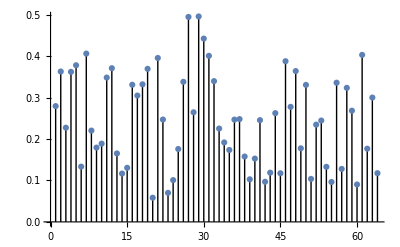

```mathematica
MyPeriodogram[seqUnfiltered-0.5]
```

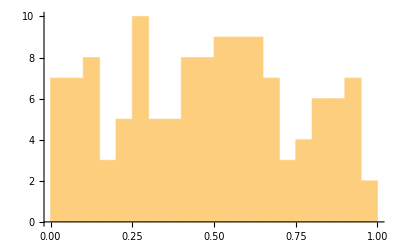

```mathematica
Histogram[seqUnfiltered,16]
```

```mathematica
(* High pass filtered version of the noise *)
```

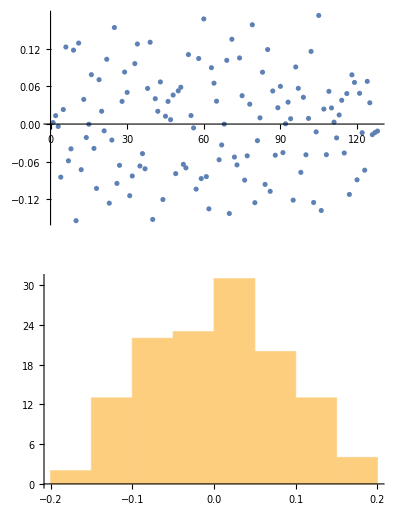

```mathematica
GraphicsGrid[{{ListPlot[MyHighpass[seqUnfiltered]]},{Histogram[MyHighpass[seqUnfiltered]]}}]
```

```mathematica
Export["afterHighpass.png",GraphicsGrid[{{ListPlot[MyHighpass[seqUnfiltered]]},{Histogram[MyHighpass[seqUnfiltered]]}}]];
```

```mathematica
RemapHistogram1D[a_]:=Module[{c,dim,b},dim=Dimensions[a][[1]];b=a;c=Sort[Table[{i,a[[i]]},{i,1,dim}],#1[[2]]<#2[[2]]&];
Do[it=c[[i,1]];b[[it]]=i/dim,{i,dim}];b]
```

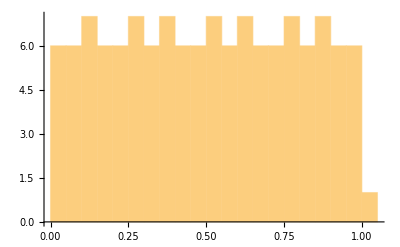

```mathematica
Histogram[RemapHistogram1D[MyHighpass[seqUnfiltered]],16]
```

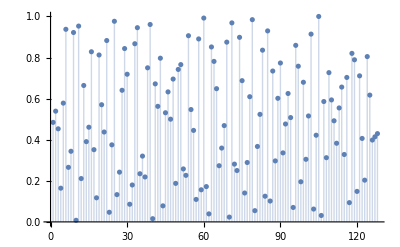

```mathematica
ListPlot[RemapHistogram1D[MyHighpass[seqUnfiltered]],Filling->Axis]
```

```mathematica
Export["afterHighpassAndRemap.png",GraphicsGrid[{{ListPlot[RemapHistogram1D[MyHighpass[seqUnfiltered]],Filling->Axis]},{Histogram[RemapHistogram1D[MyHighpass[seqUnfiltered]]]}}]];
```

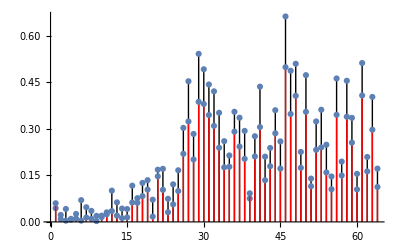

```mathematica
Show[MyPeriodogram[RemapHistogram1D[MyHighpass[seqUnfiltered]]-0.5],MyPeriodogram[MyHighpass[seqUnfiltered]*2.7,Red]]
```

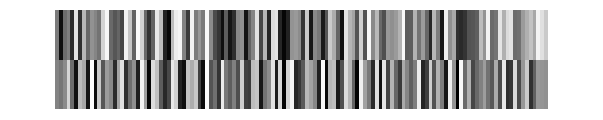

```mathematica
ArrayPlot[{seqUnfiltered,seqUnfiltered,RemapHistogram1D[MyHighpass[seqUnfiltered]],RemapHistogram1D[MyHighpass[seqUnfiltered]]}]
```

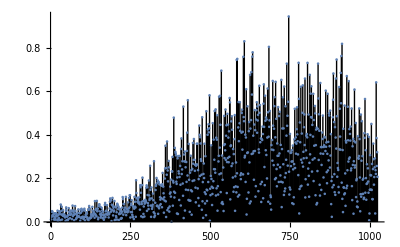

```mathematica
MyPeriodogram[RemapHistogram1D[MyHighpass[RandomReal[]&/@Range[2048]]]-0.5]
```

```mathematica
ListAnimate[{MyPeriodogram[RemapHistogram1D[MyHighpass[RandomReal[]&/@Range[2048]]]-0.5,Black,{0,1.3}],MyPeriodogram[RemapHistogram1D[MyHighpass[RemapHistogram1D[MyHighpass[RandomReal[]&/@Range[2048]]]]]-0.5,Black,{0,1.3}]}]
```

```mathematica
Export["highPassRemapTwice.gif",{MyPeriodogram[RemapHistogram1D[MyHighpass[RemapHistogram1D[MyHighpass[RandomReal[]&/@Range[2048]]]]]-0.5,Black,{0,1.3}],MyPeriodogram[RemapHistogram1D[MyHighpass[RandomReal[]&/@Range[2048]]]-0.5,Black,{0,1.3}]},"DisplayDurations"->2];
```

```mathematica
(* Like in first post, we will assume sample count of 1000 *)
sampleCount = 2000;
```

```mathematica
sineFunction[x_]:= 0.5 + Sin[x/500*2*π]*0.5;
originalSineSignal = sineFunction[#1]&/@Range[sampleCount];
(* 1 bit quantization of dithered sine signal*)
quantizedDitheredSineSignal = Round[sineFunction[#1]+RandomReal[]-0.5]&/@Range[sampleCount];
quantizedDitheredSineSignalGolden = Round[sineFunction[#1]+FractionalPart[GoldenRatio*#1]-0.5]&/@Range[sampleCount];
```

```mathematica
quantizedDitheredBlueSineSignal = Round[sineFunction[#1]&/@Range[sampleCount]+RemapHistogram1D[MyHighpass[RemapHistogram1D[MyHighpass[RemapHistogram1D[MyHighpass[RandomReal[]&/@Range[sampleCount]]]]]]]-0.5];
```

```mathematica
ArrayPlot[Join[Nest[Join[#,#,1]&,{originalSineSignal},5],Nest[Join[#,#,1]&,{quantizedDitheredSineSignal},5],
Nest[Join[#,#,1]&,{originalSineSignal},5],Nest[Join[#,#,1]&,{quantizedDitheredSineSignalGolden},5],Nest[Join[#,#,1]&,{originalSineSignal},5],
Nest[Join[#,#,1]&,{quantizedDitheredBlueSineSignal},5]]]
```

-Graphics-

```mathematica
ListAnimate[{MyPeriodogram[quantizedDitheredSineSignal-originalSineSignal,Black,{0,2.0}],MyPeriodogram[quantizedDitheredSineSignalGolden-originalSineSignal,Red,{0,2.0}],MyPeriodogram[quantizedDitheredBlueSineSignal-originalSineSignal,Green,{0,2.0}]}]
```

```mathematica
Export["HighpassRemapDitherPeriodograms.gif",{MyPeriodogram[quantizedDitheredSineSignal-originalSineSignal,Black,{0,2.0}],MyPeriodogram[quantizedDitheredSineSignalGolden-originalSineSignal,Red,{0,2.0}],MyPeriodogram[quantizedDitheredBlueSineSignal-originalSineSignal,Green,{0,2.0}]},"DisplayDurations"->2];
```

```mathematica
blueGenerated={0.46650001,0.10200000,0.59700000,0.83450001,0.34999999,0.01500000,0.57050002,0.80849999,0.19050001,0.48050001,0.93049997,0.29750001,0.63000000,0.10400000,0.79650003,0.46500000,0.22650000,0.95150000,0.55449998,0.21100000,0.81250000,0.48500001,0.03900000,0.68849999,0.26350001,0.93599999,0.40099999,0.73949999,0.07850000,0.61500001,0.28349999,0.91049999,0.51550001,0.13400000,0.80599999,0.32800001,0.61600000,0.09150000,0.83350003,0.33800000,0.59050000,0.17000000,0.93699998,0.64349997,0.34099999,0.03750000,0.58999997,0.87199998,0.48800001,0.00650000,0.30750000,0.75449997,0.43900001,0.98350000,0.23450001,0.54149997,0.79299998,0.04150000,0.42399999,0.71300000,0.23899999,0.91450000,0.57249999,0.10250000,0.39199999,0.96100003,0.57499999,0.26050001,0.76499999,0.09500000,0.49399999,0.91200000,0.24450000,0.75000000,0.46250001,0.01100000,0.68250000,0.34500000,0.85100001,0.15850000,0.64499998,0.38650000,0.96149999,0.23800001,0.74699998,0.46399999,0.02250000,0.68099999,0.26600000,0.94700003,0.41150001,0.66850001,0.14500000,0.82099998,0.49000001,0.25500000,0.98400003,0.63950002,0.18900000,0.50400001,0.83700001,0.04450000,0.42750001,0.67199999,0.19000000,0.87500000,0.36950001,0.74150002,0.12700000,0.54250002,0.83249998,0.34400001,0.02550000,0.50000000,0.90499997,0.60900003,0.05500000,0.42950001,0.73049998,0.17500000,0.88650000,0.26699999,0.67449999,0.38800001,0.91750002,0.16949999,0.65549999,0.37099999,0.90600002,0.12899999,0.47950000,0.78299999,0.14100000,0.55549997,0.91500002,0.22550000,0.46100000,0.78950000,0.05750000,0.61949998,0.33149999,0.81000000,0.05100000,0.40400001,0.60799998,0.96300000,0.18750000,0.64249998,0.33899999,0.80049998,0.01300000,0.59100002,0.23100001,0.75700003,0.31050000,0.99199998,0.40650001,0.72100002,0.13300000,0.50250000,0.91799998,0.23950000,0.74449998,0.41299999,0.01150000,0.56150001,0.87099999,0.19850001,0.65950000,0.35949999,0.83300000,0.09550000,0.43149999,0.65399998,0.99800003,0.39800000,0.18449999,0.78200001,0.50650001,0.05200000,0.69849998,0.35600001,0.88000000,0.19250000,0.52350003,0.76550001,0.01400000,0.35749999,0.60000002,0.86400002,0.10100000,0.43300000,0.70349997,0.16400000,0.83749998,0.47150001,0.22200000,0.89850003,0.60850000,0.08700000,0.45050001,0.84950000,0.27250001,0.67600000,0.05250000,0.41900000,0.93949997,0.57450002,0.24200000,0.78149998,0.03050000,0.46849999,0.72049999,0.24950001,0.93300003,0.50700003,0.12450000,0.71050000,0.29550001,0.99900001,0.65600002,0.48300001,0.00000000,0.40300000,0.74049997,0.23999999,0.94349998,0.51999998,0.15300000,0.73850000,0.43099999,0.98049998,0.27399999,0.67699999,0.09200000,0.52249998,0.85799998,0.40200001,0.02200000,0.73650002,0.24750000,0.55650002,0.95599997,0.40250000,0.12100000,0.58550000,0.94800001,0.31250000,0.64999998,0.14800000,0.90300000,0.51249999,0.27800000,0.78350002,0.06950000,0.62750000,0.28850001,0.96050000,0.39600000,0.72350001,0.10600000,0.49950001,0.88200003,0.28000000,0.66649997,0.01550000,0.45100001,0.82599998,0.16100000,0.65249997,0.34950000,0.83800000,0.17450000,0.55900002,0.95099998,0.40900001,0.16800000,0.65649998,0.99150002,0.51849997,0.32300001,0.00600000,0.78899997,0.49849999,0.17200001,0.62150002,0.98949999,0.32049999,0.64600003,0.13850001,0.85500002,0.35450000,0.63749999,0.12950000,0.82999998,0.52050000,0.22100000,0.95349997,0.39449999,0.76200002,0.11650000,0.62900001,0.35800001,0.89950001,0.25450000,0.67850000,0.05700000,0.51150000,0.83550000,0.36149999,0.04900000,0.57999998,0.90450001,0.30550000,0.69300002,0.08000000,0.49050000,0.89499998,0.23150000,0.71700001,0.44949999,0.05650000,0.81550002,0.54850000,0.23600000,0.89600003,0.49250001,0.09400000,0.70450002,0.31150001,0.90899998,0.58050001,0.03450000,0.35550001,0.65300000,0.91350001,0.16650000,0.38499999,0.84100002,0.53799999,0.11450000,0.79750001,0.32449999,0.63300002,0.11000000,0.84649998,0.35650000,0.64850003,0.15800001,0.81500000,0.42250001,0.02050000,0.56750000,0.84299999,0.19200000,0.66450000,0.31000000,0.92650002,0.50099999,0.08200000,0.68699998,0.27900001,0.88300002,0.47049999,0.13699999,0.63650000,0.95300001,0.30350000,0.56800002,0.02400000,0.76749998,0.25400001,0.56550002,0.96600002,0.42800000,0.06600000,0.69099998,0.33199999,0.75999999,0.18150000,0.92750001,0.38249999,0.66200000,0.17600000,0.82200003,0.42899999,0.01850000,0.48350000,0.86900002,0.58149999,0.00950000,0.31349999,0.76249999,0.43550000,0.97100002,0.27750000,0.61199999,0.08750000,0.80549997,0.32100001,0.59149998,0.05350000,0.73250002,0.36500001,0.89099997,0.16750000,0.55049998,0.81099999,0.38100001,0.11350000,0.87849998,0.55400002,0.25650001,0.68900001,0.06800000,0.74250001,0.33000001,0.96450001,0.49100000,0.19300000,0.81699997,0.51599997,0.05600000,0.74599999,0.26650000,0.52300000,0.92199999,0.16450000,0.67900002,0.37450001,0.89999998,0.24500000,0.59350002,0.04200000,0.70899999,0.26899999,0.94849998,0.40000001,0.66700000,0.17850000,0.92799997,0.39250001,0.67799997,0.22050001,0.89399999,0.51300001,0.09800000,0.70099998,0.34150001,0.84149998,0.12850000,0.63150001,0.28600001,0.89200002,0.49800000,0.08950000,0.77999997,0.23549999,0.66500002,0.32200000,0.97299999,0.52550000,0.15050000,0.80100000,0.33250001,0.62500000,0.07100000,0.81750000,0.25000000,0.67100000,0.39649999,0.91949999,0.16249999,0.65200001,0.30050001,0.89749998,0.48899999,0.08600000,0.69450003,0.36449999,0.88800001,0.16000000,0.71799999,0.46300000,0.22800000,0.94499999,0.56000000,0.17299999,0.76700002,0.43349999,0.06450000,0.79850000,0.53750002,0.20750000,0.89649999,0.36350000,0.63349998,0.09050000,0.78399998,0.44999999,0.17950000,0.95249999,0.56599998,0.29899999,0.78750002,0.06400000,0.61449999,0.25700000,0.95899999,0.54100001,0.27849999,0.75800002,0.08250000,0.43050000,0.93400002,0.56849998,0.14650001,0.78549999,0.28250000,0.55849999,0.90350002,0.11800000,0.44549999,0.72750002,0.29850000,0.88249999,0.14049999,0.63900000,0.36399999,0.86600000,0.15899999,0.64899999,0.30599999,0.98150003,0.59399998,0.34850001,0.01950000,0.72250003,0.41800001,0.93000001,0.20900001,0.53299999,0.75749999,0.07250000,0.37650001,0.86849999,0.53100002,0.08300000,0.69999999,0.30100000,0.91850001,0.50150001,0.10750000,0.70300001,0.35100001,0.86799997,0.13150001,0.50849998,0.76999998,0.16900000,0.39950001,0.97950000,0.65799999,0.17700000,0.52149999,0.92000002,0.39850000,0.12500000,0.74900001,0.46450001,0.06100000,0.80199999,0.52899998,0.20150000,0.90750003,0.38900000,0.66250002,0.19900000,0.91549999,0.40700001,0.68000001,0.02900000,0.34599999,0.83899999,0.61250001,0.06700000,0.43650001,0.87300003,0.29499999,0.72549999,0.03600000,0.60549998,0.32400000,0.80900002,0.05300000,0.46149999,0.70999998,0.21799999,0.94550002,0.38600001,0.71350002,0.10950000,0.42699999,0.93099999,0.54799998,0.12650000,0.71550000,0.30199999,0.89700001,0.45150000,0.05550000,0.57950002,0.81800002,0.19700000,0.48449999,0.95400000,0.24850000,0.73350000,0.48150000,0.09750000,0.86199999,0.36750001,0.66799998,0.24900000,0.83499998,0.12250000,0.64050001,0.38299999,0.92250001,0.20400000,0.70950001,0.43750000,0.03700000,0.79500002,0.50999999,0.25099999,0.98000002,0.56250000,0.21400000,0.82700002,0.47749999,0.06550000,0.69900000,0.37799999,0.92299998,0.20600000,0.69950002,0.42649999,0.03100000,0.79100001,0.54200000,0.21150000,0.90649998,0.37050000,0.73100001,0.02450000,0.58700001,0.21900000,0.75950003,0.33950001,0.99650002,0.55599999,0.20350000,0.80750000,0.45649999,0.04500000,0.69250000,0.31200001,0.95850003,0.52950001,0.17800000,0.77800000,0.41400000,0.02150000,0.57849997,0.86100000,0.22350000,0.45449999,0.79200000,0.07200000,0.61000001,0.25549999,0.92500001,0.39500001,0.74949998,0.10850000,0.62400001,0.29949999,0.94300002,0.52499998,0.15500000,0.83200002,0.35150000,0.65100002,0.18000001,0.84350002,0.54750001,0.02700000,0.36849999,0.86549997,0.54500002,0.14200000,0.81050003,0.32900000,0.68449998,0.00400000,0.44749999,0.73799998,0.20999999,0.92400002,0.37250000,0.64950001,0.15700001,0.90950000,0.53700000,0.26949999,0.75099999,0.06500000,0.48750001,0.87800002,0.22400001,0.54299998,0.78799999,0.11700000,0.46599999,0.91100001,0.30250001,0.70150000,0.09900000,0.50449997,0.93550003,0.31500000,0.70499998,0.12350000,0.44900000,0.97649997,0.63200003,0.32350001,0.02000000,0.71399999,0.40549999,0.90399998,0.19100000,0.66949999,0.41100001,0.98449999,0.28749999,0.71499997,0.15099999,0.51400000,0.81400001,0.03150000,0.32150000,0.73699999,0.44150001,0.99400002,0.29650000,0.72600001,0.06000000,0.56300002,0.26499999,0.99100000,0.65450001,0.40750000,0.10500000,0.86750001,0.54049999,0.26449999,0.71450001,0.14450000,0.89800000,0.52200001,0.21750000,0.80949998,0.45500001,0.01450000,0.68750000,0.34050000,0.85200000,0.14749999,0.66350001,0.39399999,0.94050002,0.27149999,0.70400000,0.02950000,0.56500000,0.26550001,0.96200001,0.67400002,0.34650001,0.00100000,0.48550001,0.68949997,0.99449998,0.42050001,0.10700000,0.75400001,0.25200000,0.57900000,0.98250002,0.44000000,0.13500001,0.79549998,0.32749999,0.69499999,0.06650000,0.49700001,0.88849998,0.29249999,0.63050002,0.10550000,0.82499999,0.33649999,0.59750003,0.04800000,0.78700000,0.29200000,0.54949999,0.94650000,0.19450000,0.45950001,0.78649998,0.07500000,0.62300003,0.29300001,0.93500000,0.58649999,0.13950001,0.47350001,0.78600001,0.00750000,0.41549999,0.68049997,0.14900000,0.75900000,0.40599999,0.96749997,0.20800000,0.76450002,0.33550000,0.62800002,0.14150000,0.81199998,0.42150000,0.03850000,0.57099998,0.88050002,0.28099999,0.60149997,0.06850000,0.74199998,0.39150000,0.92850000,0.21600001,0.51099998,0.81950003,0.13200000,0.65149999,0.31750000,0.98750001,0.54350001,0.25749999,0.77300000,0.01250000,0.45249999,0.69650000,0.18550000,0.92900002,0.30700001,0.56099999,0.77200001,0.07900000,0.36899999,0.85650003,0.59899998,0.03400000,0.42500001,0.74750000,0.22000000,0.98549998,0.53850001,0.29100001,0.74800003,0.04050000,0.47700000,0.82749999,0.17749999,0.66000003,0.28900000,0.98650002,0.60600001,0.36600000,0.07300000,0.81650001,0.60049999,0.15950000,0.41650000,0.95950001,0.57300001,0.15650000,0.78049999,0.46900001,0.20500000,0.96550000,0.57550001,0.24650000,0.87449998,0.50300002,0.15400000,0.77950001,0.42350000,0.02350000,0.56050003,0.87650001,0.20000000,0.74000001,0.28999999,0.56650001,0.96799999,0.18650000,0.50800002,0.81449997,0.35850000,0.05150000,0.60650003,0.88900000,0.40050000,0.16200000,0.79000002,0.57200003,0.00900000,0.41700000,0.74349999,0.24550000,0.92350000,0.50950003,0.09300000,0.69199997,0.33750001,0.82849997,0.07150000,0.46349999,0.70599997,0.20200001,0.94400001,0.30849999,0.73600000,0.48100001,0.06050000,0.82400000,0.26750001,0.54650003,0.78100002,0.09850000,0.37700000,0.88550001,0.55299997,0.11950000,0.77749997,0.26150000,0.58200002,0.99949998,0.44800001,0.22950000,0.73549998,0.03300000,0.48850000,0.84600002,0.27599999,0.61799997,0.03250000,0.77499998,0.26850000,0.54400003,0.84249997,0.13800000,0.46799999,0.88450003,0.29400000,0.70700002,0.00450000,0.38350001,0.57749999,0.93199998,0.17399999,0.64550000,0.33600000,0.80699998,0.04850000,0.41049999,0.61150002,0.98850000,0.28299999,0.68800002,0.09600000,0.43000001,0.91900003,0.65899998,0.06350000,0.35350001,0.61350000,0.88400000,0.15549999,0.40500000,0.66900003,0.99299997,0.29600000,0.60450000,0.13650000,0.87900001,0.51800001,0.27300000,0.77700001,0.04100000,0.60750002,0.24699999,0.90700001,0.39550000,0.67350000,0.18200000,0.94250000,0.52700001,0.27700001,0.76849997,0.01650000,0.46050000,0.71950001,0.24300000,0.94000000,0.50749999,0.14250000,0.81849998,0.33350000,0.69150001,0.10350000,0.45899999,0.97200000,0.63499999,0.14350000,0.46550000,0.89050001,0.28450000,0.68150002,0.04550000,0.48400000,0.86350000,0.28200001,0.68199998,0.02650000,0.46000001,0.83099997,0.14850000,0.64150000,0.34349999,0.80350000,0.13249999,0.43799999,0.94450003,0.63099998,0.09350000,0.44499999,0.76349998,0.32550001,0.96350002,0.20050000,0.69400001,0.41850001,0.04000000,0.81150001,0.48699999,0.18700001,0.66299999,0.98900002,0.30649999,0.59850001,0.10800000,0.75250000,0.39100000,0.94950002,0.22149999,0.70200002,0.44049999,0.05000000,0.79699999,0.50599998,0.23199999,0.87550002,0.58300000,0.04400000,0.35400000,0.84750003,0.52649999,0.10150000,0.70550001,0.30500001,0.93150002,0.50900000,0.12200000,0.70050001,0.28700000,0.99599999,0.45350000,0.76400000,0.33050001,0.00200000,0.56950003,0.85549998,0.21300000,0.67650002,0.31450000,0.97399998,0.49300000,0.17350000,0.86299998,0.55150002,0.25900000,0.74500000,0.06150000,0.49500000,0.89300001,0.23300000,0.70800000,0.45199999,0.02800000,0.73750001,0.39050001,0.92449999,0.25999999,0.62449998,0.09450000,0.79900002,0.46950001,0.23700000,0.93750000,0.62250000,0.13450000,0.48949999,0.82450002,0.34000000,0.01700000,0.58099997,0.86250001,0.21450000,0.45400000,0.73400003,0.18300000,0.96950001,0.53500003,0.30149999,0.78450000,0.05900000,0.62699997,0.28549999,0.88099998,0.45800000,0.10650000,0.60200000,0.84850001,0.36050001,0.01200000,0.47650000,0.87349999,0.57800001,0.21950001,0.99349999,0.52850002,0.30899999,0.83600003,0.16500001,0.72399998,0.44400001,0.01350000,0.69050002,0.30450001,0.90850002,0.51700002,0.11200000,0.76950002,0.29449999,0.53950000,0.99500000,0.23400000,0.71600002,0.47900000,0.03500000,0.82249999,0.33300000,0.62199998,0.08500000,0.74650002,0.31850001,0.96850002,0.52450001,0.15449999,0.81599998,0.34549999,0.64450002,0.15350001,0.90249997,0.51499999,0.27950001,0.77899998,0.03800000,0.62099999,0.32949999,0.80299997,0.14300001,0.49900001,0.96649998,0.32650000,0.76599997,0.22849999,0.59450001,0.04350000,0.80500001,0.34299999,0.62849998,0.13550000,0.85600001,0.35900000,0.61650002,0.15000001,0.88950002,0.37500000,0.66049999,0.18099999,0.83649999,0.44850001,0.07000000,0.61100000,0.84799999,0.21550000,0.52399999,0.92949998,0.38949999,0.12750000,0.62550002,0.93250000,0.43500000,0.11250000,0.69349998,0.28799999,0.97799999,0.60100001,0.37000000,0.06200000,0.80800003,0.55800003,0.31400001,0.91600001,0.19750001,0.72649997,0.42550001,0.00500000,0.58450001,0.80400002,0.20450000,0.41249999,0.99699998,0.68650001,0.23750000,0.56349999,0.02100000,0.80000001,0.47600001,0.13000000,0.71649998,0.31549999,0.96399999,0.49200001,0.17250000,0.86699998,0.55350000,0.26800001,0.74849999,0.02600000,0.47250000,0.82800001,0.24150001,0.56999999,0.95649999,0.18250000,0.51450002,0.82650000,0.37599999,0.03650000,0.76800001,0.46700001,0.14550000,0.59500003,0.97600001,0.31950000,0.69550002,0.09650000,0.42300001,0.91649997,0.61900002,0.13050000,0.38400000,0.91299999,0.57700002,0.14000000,0.77850002,0.45750001,0.21650000,0.90200001,0.54000002,0.13100000,0.72149998,0.39700001,0.95700002,0.21500000,0.53899997,0.78500003,0.12000000,0.47400001,0.89899999,0.28950000,0.69749999,0.04700000,0.40450001,0.86150002,0.59549999,0.04650000,0.32499999,0.88150001,0.41200000,0.75550002,0.08800000,0.61699998,0.28049999,0.88349998,0.50199997,0.07650000,0.76150000,0.27550000,0.55949998,0.90100002,0.12400000,0.44600001,0.72899997,0.23500000,0.98699999,0.54699999,0.31099999,0.82150000,0.12050000,0.64099997,0.39750001,0.93900001,0.27200001,0.71850002,0.00350000,0.44350001,0.68400002,0.19800000,0.93449998,0.38749999,0.73000002,0.07050000,0.60250002,0.25350001,0.92150003,0.38000000,0.71749997,0.11600000,0.52600002,0.90050000,0.23000000,0.49599999,0.84700000,0.17649999,0.69599998,0.47200000,0.06250000,0.82050002,0.33399999,0.70249999,0.11400000,0.54900002,0.90549999,0.40349999,0.10300000,0.77149999,0.50500000,0.22250000,0.98199999,0.63800001,0.42449999,0.03000000,0.76899999,0.29150000,0.55699998,0.95749998,0.20850000,0.48649999,0.75849998,0.00250000,0.35249999,0.58899999,0.95999998,0.27450001,0.68300003,0.05450000,0.48199999,0.85750002,0.27050000,0.60949999,0.04750000,0.78250003,0.26400000,0.58950001,0.98299998,0.42600000,0.11500000,0.70749998,0.32699999,0.97700000,0.53450000,0.17900001,0.77399999,0.48600000,0.08850000,0.83399999,0.34799999,0.63450003,0.15750000,0.81900001,0.44299999,0.05400000,0.57150000,0.85949999,0.18850000,0.62000000,0.29699999,0.99550003,0.68599999,0.36550000,0.00850000,0.54449999,0.83950001,0.19949999,0.67949998,0.32850000,0.97450000,0.51650000,0.16300000,0.82550001,0.34750000,0.72500002,0.02750000,0.58749998,0.32600001,0.80150002,0.04250000,0.40950000,0.59799999,0.98799998,0.24250001,0.75199997,0.43849999,0.03550000,0.58850002,0.85000002,0.37200001,0.08550000,0.58499998,0.93849999,0.26199999,0.75500000,0.53600001,0.00050000,0.35200000,0.66750002,0.98500001,0.29049999,0.59200001,0.12549999,0.86000001,0.36199999,0.66100001,0.20250000,0.87400001,0.56449997,0.01600000,0.42100000,0.77249998,0.14700000,0.51050001,0.86650002,0.22499999,0.53049999,0.91700000,0.16850001,0.65050000,0.36250001,0.87250000,0.13600001,0.49550000,0.79449999,0.19400001,0.55250001,0.97250003,0.30800000,0.63849998,0.12600000,0.85250002,0.35299999,0.64749998,0.17100000,0.84899998,0.50050002,0.05050000,0.68349999,0.33500001,0.81999999,0.07350000,0.47499999,0.71100003,0.21200000,0.95499998,0.38699999,0.65750003,0.18400000,0.84399998,0.45699999,0.08450000,0.60399997,0.86949998,0.15600000,0.44650000,0.72950000,0.22600000,0.87750000,0.45300001,0.08900000,0.52100003,0.95200002,0.25150001,0.72850001,0.48249999,0.08150000,0.84050000,0.34900001,0.64399999,0.17150000,0.86049998,0.49349999,0.11300000,0.80650002,0.34250000,0.63400000,0.09700000,0.82950002,0.25049999,0.67750001,0.40799999,0.97750002,0.27350000,0.68550003,0.06300000,0.51899999,0.86449999,0.20100001,0.44700000,0.77050000,0.01900000,0.59249997,0.23649999,0.77550000,0.41000000,0.99049997,0.28650001,0.71200001,0.14399999,0.56699997,0.92549998,0.41999999,0.08650000,0.69700003,0.37750000,0.89249998,0.16550000,0.51200002,0.83999997,0.26249999,0.61849999,0.05800000,0.79250002,0.49649999,0.17550001,0.89349997,0.36700001,0.66149998,0.19149999,0.87949997,0.47549999,0.09000000,0.71149999,0.37900001,0.91000003,0.25250000,0.60699999,0.03350000,0.72200000,0.37300000,0.87599999,0.16050000,0.64300001,0.35699999,0.84200001,0.11900000,0.62599999,0.25950000,0.92600000,0.38850001,0.67500001,0.19599999,0.95800000,0.41350001,0.77100003,0.22900000,0.58399999,0.00550000,0.70850003,0.34450001,0.81300002,0.07800000,0.41450000,0.63599998,0.99250001,0.28150001,0.59600002,0.08100000,0.79049999,0.47000000,0.23050000,0.93349999,0.56199998,0.15200000,0.73150003,0.37149999,0.94199997,0.20649999,0.52749997,0.76650000,0.07400000,0.37349999,0.84549999,0.59299999,0.00700000,0.31299999,0.75300002,0.43599999,0.97549999,0.20299999,0.67049998,0.37400001,0.94999999,0.27000001,0.62050003,0.18350001,0.94099998,0.66399997,0.36300001,0.02500000,0.56900001,0.88599998,0.30300000,0.62650001,0.08400000,0.80449998,0.30399999,0.56400001,0.92699999,0.16350000,0.44200000,0.69000000,0.11550000,0.87150002,0.29800001,0.55000001,0.79350001,0.10000000,0.44100001,0.85850000,0.19550000,0.68500000,0.41949999,0.98100001,0.27500001,0.61549997,0.09950000,0.74400002,0.31700000,0.94900000,0.51749998,0.13900000,0.72700000,0.38200000,0.94749999,0.16150001,0.63249999,0.25799999,0.82900000,0.55199999,0.01750000,0.36100000,0.85900003,0.54549998,0.14950000,0.81349999,0.33100000,0.67549998,0.04300000,0.47450000,0.84450001,0.18050000,0.65350002,0.36649999,0.85299999,0.09250000,0.47799999,0.72299999,0.21250001,0.97049999,0.53549999,0.26300001,0.73500001,0.02850000,0.47099999,0.82300001,0.15150000,0.63999999,0.28400001,0.88749999,0.46200001,0.10450000,0.78850001,0.54600000,0.23250000,0.99000001,0.43200001,0.75349998,0.31650001,0.00150000,0.55500001,0.85450000,0.21050000,0.67250001,0.38550001,0.94599998,0.25850001,0.61299998,0.07600000,0.73199999,0.31799999,0.98600000,0.53149998,0.25299999,0.74550003,0.04950000,0.47850001,0.85350001,0.19499999,0.66600001,0.38999999,0.96249998,0.21699999,0.72450000,0.45550001,0.14600000,0.87050003,0.37950000,0.63550001,0.03950000,0.79400003,0.24400000,0.67299998,0.39899999,0.97350001,0.27100000,0.63700002,0.12300000,0.83050001,0.45850000,0.17050000,0.64649999,0.96899998,0.23850000,0.46750000,0.72799999,0.16599999,0.95050001,0.52800000,0.28500000,0.79949999,0.07700000,0.69800001,0.45600000,0.24050000,0.99750000,0.65499997,0.47999999,0.07550000,0.79600000,0.33450001,0.59950000,0.02300000,0.75650001,0.24349999,0.43950000,0.99849999,0.58350003,0.25600001,0.75599998,0.07750000,0.49450001,0.89450002,0.23350000,0.72000003,0.43450001,0.11750000,0.87000000,0.60500002,0.34200001,0.01000000,0.71249998,0.42199999,0.93800002,0.22450000,0.74299997,0.43250000,0.08050000,0.61400002,0.92100000,0.24100000,0.50349998,0.77649999,0.07450000,0.44450000,0.85149997,0.20950000,0.53250003,0.80250001,0.04600000,0.42850000,0.70649999,0.21349999,0.97000003,0.53649998,0.29350001,0.79799998,0.10050000,0.64200002,0.37549999,0.95450002,0.21850000,0.74100000,0.51349998,0.16700000,0.96499997,0.43700001,0.76050001,0.32249999,0.00800000,0.58249998,0.83850002,0.37850001,0.08350000,0.60299999,0.91399997,0.30000001,0.58600003,0.09100000,0.82349998,0.35049999,0.61750001,0.12800001,0.87699997,0.36800000,0.67000002,0.22750001,0.95550001,0.53399998,0.18799999,0.79149997,0.43399999,0.06900000,0.61049998,0.88700002,0.38450000,0.11150000,0.73449999,0.47299999,0.93650001,0.33849999,0.03200000,0.55100000,0.85399997,0.19650000,0.66549999,0.31900001,0.97149998,0.53200001,0.15250000,0.83149999,0.34700000,0.65850002,0.20550001,0.89550000,0.57650000,0.06750000,0.44250000,0.85049999,0.18950000,0.67150003,0.38150001,0.91149998,0.19350000,0.51950002,0.75050002,0.01050000,0.35499999,0.58800000,0.97500002,0.24600001,0.76300001,0.55750000,0.00300000,0.41749999,0.73900002,0.22700000,0.88999999,0.50550002,0.07950000,0.75150001,0.24800000,0.52999997,0.97899997,0.31999999,0.64700001,0.13349999,0.85699999,0.36000001,0.65700001,0.18600000,0.88499999,0.49149999,0.11100000,0.73299998,0.41499999,0.89150000,0.33700001,0.05950000,0.60350001,0.86500001,0.38049999,0.12150000,0.62349999,0.90149999,0.39350000,0.13750000,0.62949997,0.92049998,0.40849999,0.11850000,0.77450001,0.53350002,0.18500000,0.90799999,0.30950001,0.57599998,0.84500003,0.11050000,0.39300001,0.64800000,0.97850001,0.27649999,0.57400000,0.05850000,0.77600002,0.26100001,0.57349998,0.96700001,0.40149999,0.10900000,0.71899998,0.41600001,0.94150001,0.20700000,0.49750000,0.77350003,0.01800000,0.59649998,0.22300000,0.76099998,0.31600001,0.91250002};
```

```mathematica
quantizedDitheredBlueGeneratedSineSignal = Round[sineFunction[#1]&/@Range[sampleCount]+blueGenerated-0.5];
```

```mathematica
ListAnimate[{MyPeriodogram[quantizedDitheredSineSignal-originalSineSignal,Black,{0,2.0}],MyPeriodogram[quantizedDitheredSineSignalGolden-originalSineSignal,Red,{0,2.0}],MyPeriodogram[quantizedDitheredBlueSineSignal-originalSineSignal,Green,{0,2.0}],MyPeriodogram[quantizedDitheredBlueGeneratedSineSignal-originalSineSignal,Yellow,{0,2.0}]}]
```

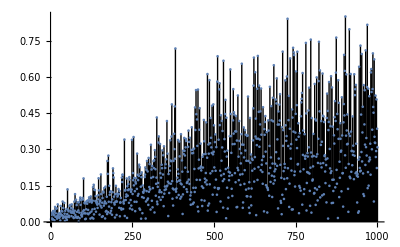

```mathematica
MyPeriodogram[blueGenerated-0.5]
```

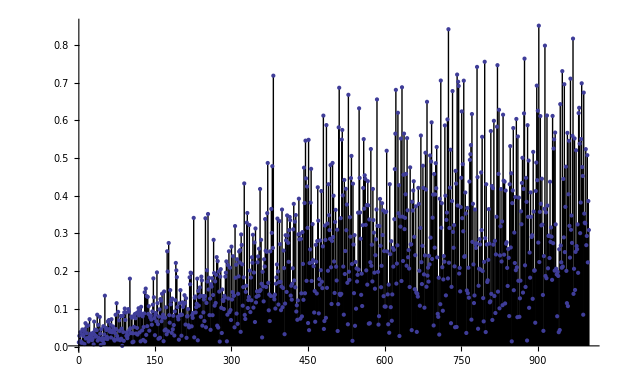

-Graphics-

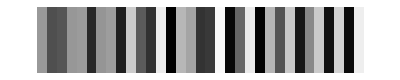

```mathematica
(*Example of problems with highpass and remap - some patterns remain locally *)
ArrayPlot[{Nest[RemapHistogram1D[MyHighpass[#]]&,RandomReal[]&/@Range[128],10][[32;;64]]}]
```

```mathematica
ArrayPlot[Join[Nest[Join[#,#,1]&,{originalSineSignal},5],Nest[Join[#,#,1]&,{quantizedDitheredSineSignal},5],
Nest[Join[#,#,1]&,{originalSineSignal},5],Nest[Join[#,#,1]&,{quantizedDitheredSineSignalGolden},5],Nest[Join[#,#,1]&,{originalSineSignal},5],
Nest[Join[#,#,1]&,{quantizedDitheredBlueSineSignal},5],Nest[Join[#,#,1]&,{originalSineSignal},5],Nest[Join[#,#,1]&,{quantizedDitheredBlueGeneratedSineSignal},5]]]
```

-Graphics-

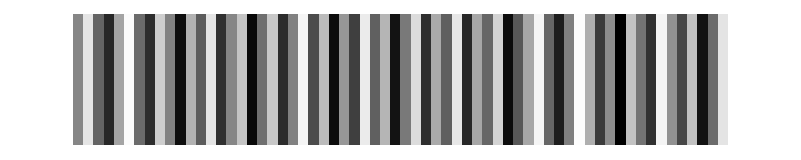

```mathematica
ArrayPlot[{blueGenerated[[1;;64]]}]
```

```mathematica
ListAnimate[{MyPeriodogram[blueGenerated-0.5,Red,{0,1}],MyPeriodogram[RemapHistogram1D[MyHighpass[RandomReal[]&/@Range[2000]]]-0.5,Black,{0,1}]}]
```

```mathematica
Export["highpassremapvsgenerated.gif",{MyPeriodogram[blueGenerated-0.5,Red,{0,1}],MyPeriodogram[RemapHistogram1D[MyHighpass[RandomReal[]&/@Range[2000]]]-0.5,Black,{0,1}]},"DisplayDurations"->2];
```

```mathematica
Export["all1dtechniquescomparedfrequencies.gif",{MyPeriodogram[quantizedDitheredSineSignal-originalSineSignal,Black,{0,2.0}],MyPeriodogram[quantizedDitheredSineSignalGolden-originalSineSignal,Red,{0,2.0}],MyPeriodogram[quantizedDitheredBlueSineSignal-originalSineSignal,Green,{0,2.0}],MyPeriodogram[quantizedDitheredBlueGeneratedSineSignal-originalSineSignal,Yellow,{0,2.0}]},"DisplayDurations"->2];
```